### Results from a calculation of K from the kappa J-V relation assuming 1≪ϕ^—≪R_B.

```mathematica
ratio[κ_]:=Gamma[κ]/((κ-3/2)^(1/2)Gamma[κ-1/2])
```

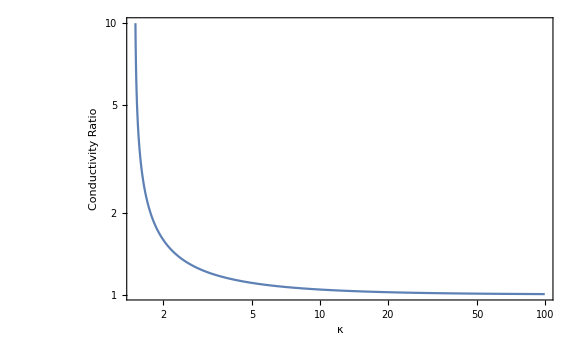

```mathematica
LogLogPlot[ratio[κ],{κ,3/2,100},PlotRange->{{3/2,100},{1,10}},LabelStyle->Directive[Larger],FrameLabel->{κ,StringForm["Conductivity Ratio"]},Frame->True,ImageSize->Large]
```

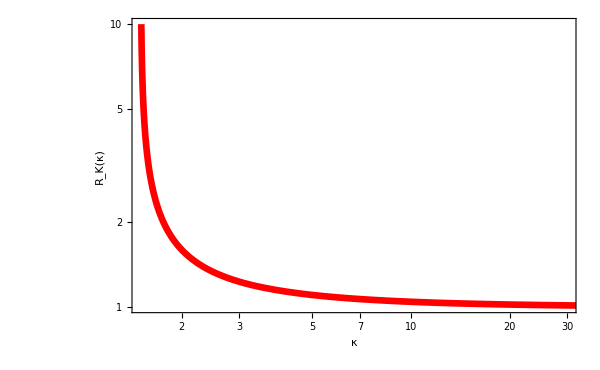

```mathematica
LogLogPlot[ratio[κ],{κ,3/2,100},PlotRange->{{1.5,30},{1,10}},PlotStyle->Directive[Red,Thickness[0.008]],LabelStyle->(FontSize->18),FrameLabel->{κ,StringForm["R_K(κ)"]},Frame->True,ImageSize->600]
```